## Function Definitions

Don’t forget that there’s also an omega floating around

### For m = 0

```mathematica
const1=1/(2*Pi)
```

1/(2 π)

```mathematica
p0[e_,s_]:=const1*Integrate[Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi},Assumptions->{Element[e,Reals],e>0}]
```

```mathematica
Np0[e_,s_]:=const1*NIntegrate[Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi}]
```

```mathematica
p0NoPole[e_,s_]:=const1*Integrate[(1-e^2)^(3/2)*Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi},Assumptions->{e≥0,e≤1,Element[s,Integers]}]
```

```mathematica
Np0NoPole[e_,s_]:=const1*NIntegrate[(1-e^2)^(3/2)*Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi}]
```

### For m = 2

There’s also an Exp[phi_not]
Apparently that’s actually handled in POET, never mind

```mathematica
const2=1
```

1

#### Sub integrals

```mathematica
pTwoA[e_,s_]:=const1*(1-e^2)*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4),{u,0,2*Pi},Assumptions->{Element[e,Reals],e>0}]
```

```mathematica
pTwoB[e_,s_]:=const1*(1-e^2)*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Cos[2*u],{u,0,2*Pi},Assumptions->{Element[e,Reals],e>0}]
```

```mathematica
pTwoC[e_,s_]:=const1*I*Sqrt[(1-e^2)]*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[2*u],{u,0,2*Pi},Assumptions->{Element[e,Reals],e>0}]
```

```mathematica
pTwoD[e_,s_]:=const1*I*2*e*Sqrt[(1-e^2)]*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[u],{u,0,2*Pi},Assumptions->{Element[e,Reals],e>0}]
```

#### Main Coefficients

I’m not sure why I’m dividing by const1, but I don’t believe it’s causing any issues w/ regard to behavior, so I’m just going to leave it for now

```mathematica
pPlus2[e_,s_]:=(1/(const1*const2))*(p0[e,s]-pTwoA[e,s]+pTwoB[e,s]-pTwoC[e,s]+pTwoD[e,s])
```

```mathematica
pPlus2Ltd[e_,s_]:=(1/(const1*const2))*(0-pTwoA[e,s]+pTwoB[e,s]-pTwoC[e,s]+pTwoD[e,s])
```

```mathematica
pMinus2[e_,s_]:=(const2/const1)*(p0[e,s]-pTwoA[e,s]+pTwoB[e,s]+pTwoC[e,s]-pTwoD[e,s])
```

#### Also numerical integration versions

```mathematica
NpTwoA[e_,s_]:=const1*(1-e^2)*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4),{u,0,2*Pi}]
```

```mathematica
NpTwoB[e_,s_]:=const1*(1-e^2)*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Cos[2*u],{u,0,2*Pi}]
```

```mathematica
NpTwoC[e_,s_]:=const1*I*Sqrt[(1-e^2)]*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[2*u],{u,0,2*Pi}]
```

```mathematica
NpTwoD[e_,s_]:=const1*I*2*e*Sqrt[(1-e^2)]*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[u],{u,0,2*Pi}]
```

```mathematica
NpPlus2[e_,s_]:=(1/(const1*const2))*(Np0[e,s]-NpTwoA[e,s]+NpTwoB[e,s]-NpTwoC[e,s]+NpTwoD[e,s])
```

```mathematica
NpMinus2[e_,s_]:=(const2/const1)*(Np0[e,s]-NpTwoA[e,s]+NpTwoB[e,s]+NpTwoC[e,s]-NpTwoD[e,s])
```

```mathematica
NpPlus2NP[e_,s_]:=((1-e^2)^(3/2)/(const1*const2))*(Np0[e,s]-NpTwoA[e,s]+NpTwoB[e,s]-NpTwoC[e,s]+NpTwoD[e,s])
```

```mathematica
NpMinus2NP[e_,s_]:=((1-e^2)^(3/2))*(const2/const1)*(Np0[e,s]-NpTwoA[e,s]+NpTwoB[e,s]+NpTwoC[e,s]-NpTwoD[e,s])
```

## Verifying Values

```mathematica
p0[e,0]
```

ConditionalExpression[1/((1-e^2)^(3/2)),0<e<1]

```mathematica
p0NoPole[e,0]
```

ConditionalExpression[1,0<e<1]

```mathematica
pPlus2[e,0]
```

ConditionalExpression[2 ((5 e^2)/(2 (1-e^2)^(5/2))+1/((1-e^2)^(3/2))-(2+3 e^2)/(2 (1-e^2)^(5/2))) ⅇ^(-2 ⅈ) π,0<e<1]

```mathematica
FullSimplify[ConditionalExpression[2 ((5 e^2)/(2 (1-e^2)^(5/2))+1/((1-e^2)^(3/2))-(2+3 e^2)/(2 (1-e^2)^(5/2))) ⅇ^(-2 ⅈ) π,0<e<1]]
```

ConditionalExpression[0,0<e<1]

```mathematica
FullSimplify[pMinus2[e,0]]
```

ConditionalExpression[0,0<e<1]

## What do these things do without the p_0s?

i did not make a mistake i thought i made, sweet

### W/o the factor

hi

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

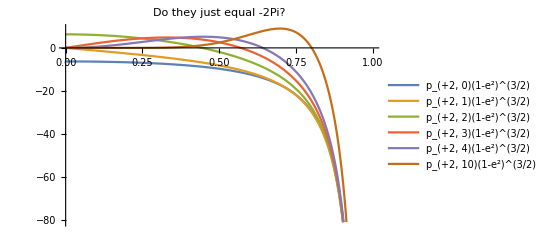

```mathematica
Plot[{Re[NpPlus2[e,0]-(1/(const1*const2))*Np0[e,0]],Re[NpPlus2[e,1]-(1/(const1*const2))*Np0[e,1]],Re[NpPlus2[e,2]-(1/(const1*const2))*Np0[e,2]],Re[NpPlus2[e,3]-(1/(const1*const2))*Np0[e,3]],Re[NpPlus2[e,4]-(1/(const1*const2))*Np0[e,4]],Re[NpPlus2[e,10]-(1/(const1*const2))*Np0[e,10]]},{e,0,1},PlotLegends->{"p_(+2, 0)(1-e^2)^(3/2)","p_(+2, 1)(1-e^2)^(3/2)","p_(+2, 2)(1-e^2)^(3/2)","p_(+2, 3)(1-e^2)^(3/2)","p_(+2, 4)(1-e^2)^(3/2)","p_(+2, 10)(1-e^2)^(3/2)"},PlotLabel->"Do they just equal -2Pi?"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

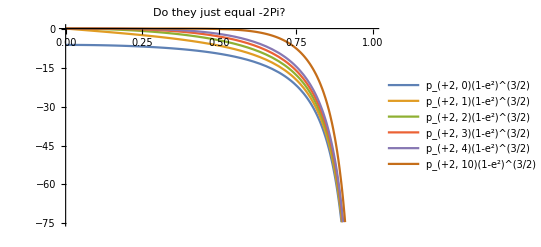

```mathematica
Plot[{Re[NpMinus2[e,0]-(1/(const1*const2))*Np0[e,0]],Re[NpMinus2[e,1]-(1/(const1*const2))*Np0[e,1]],Re[NpMinus2[e,2]-(1/(const1*const2))*Np0[e,2]],Re[NpMinus2[e,3]-(1/(const1*const2))*Np0[e,3]],Re[NpMinus2[e,4]-(1/(const1*const2))*Np0[e,4]],Re[NpMinus2[e,10]-(1/(const1*const2))*Np0[e,10]]},{e,0,1},PlotLegends->{"p_(+2, 0)(1-e^2)^(3/2)","p_(+2, 1)(1-e^2)^(3/2)","p_(+2, 2)(1-e^2)^(3/2)","p_(+2, 3)(1-e^2)^(3/2)","p_(+2, 4)(1-e^2)^(3/2)","p_(+2, 10)(1-e^2)^(3/2)"},PlotLabel->"Do they just equal -2Pi?"]
```

### W/ the factor

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

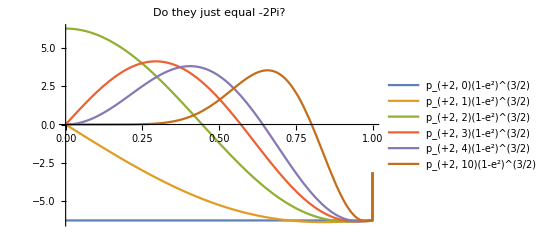

```mathematica
Plot[{Re[NpPlus2NP[e,0]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,0]],Re[NpPlus2NP[e,1]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,1]],Re[NpPlus2NP[e,2]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,2]],Re[NpPlus2NP[e,3]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,3]],Re[NpPlus2NP[e,4]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,4]],Re[NpPlus2NP[e,10]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,10]]},{e,0,1},PlotLegends->{"p_(+2, 0)(1-e^2)^(3/2)","p_(+2, 1)(1-e^2)^(3/2)","p_(+2, 2)(1-e^2)^(3/2)","p_(+2, 3)(1-e^2)^(3/2)","p_(+2, 4)(1-e^2)^(3/2)","p_(+2, 10)(1-e^2)^(3/2)"},PlotLabel->"Do they just equal -2Pi?"]
```

```mathematica
FullSimplify[(pPlus2[e,0]-(1/(const1*const2))*p0[e,0])*(1-e^2)^(3/2)]
```

ConditionalExpression[-2 π,e<1]

So yes, they do just equal -2Pi, which of course they needed to in order to cancel out p_0s.

```mathematica
FullSimplify[(pPlus2[e,1]-(1/(const1*const2))*p0[e,1])*(1-e^2)^(3/2)]
```

$Aborted

```mathematica
FullSimplify[pPlus2[e,0]]
```

ConditionalExpression[0,e<1]

```mathematica
FullSimplify[pPlus2Ltd[e,0]]
```

ConditionalExpression[-(2 π)/((1-e^2)^(3/2)),e<1]

```mathematica
FullSimplify[Series[(pPlus2Ltd[e,1])*(1-e^2)^(3/2),{e,0,5}]]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^4 does not converge on {0, 2\ π}.

What about the negatives? Probably.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

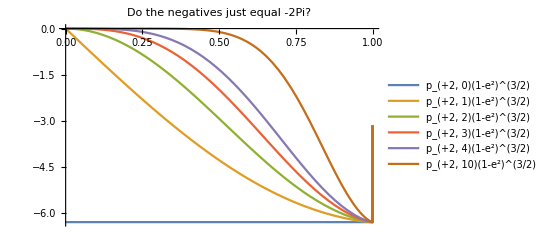

```mathematica
Plot[{Re[NpMinus2NP[e,0]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,0]],Re[NpMinus2NP[e,1]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,1]],Re[NpMinus2NP[e,2]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,2]],Re[NpMinus2NP[e,3]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,3]],Re[NpMinus2NP[e,4]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,4]],Re[NpMinus2NP[e,10]-((1-e^2)^(3/2)/(const1*const2))*Np0[e,10]]},{e,0,1},PlotLegends->{"p_(+2, 0)(1-e^2)^(3/2)","p_(+2, 1)(1-e^2)^(3/2)","p_(+2, 2)(1-e^2)^(3/2)","p_(+2, 3)(1-e^2)^(3/2)","p_(+2, 4)(1-e^2)^(3/2)","p_(+2, 10)(1-e^2)^(3/2)"},PlotLabel->"Do the negatives just equal -2Pi?"]
```

```mathematica
FullSimplify[(pMinus2[e,0]-(1/(const1*const2))*p0[e,0])*(1-e^2)^(3/2)]
```

ConditionalExpression[-2 π,e<1]

Yeet.

## Shape of m=+2 feat. Ed Sheeran

```mathematica
p0[e,1]
```

$Aborted

```mathematica
Np0NoPole[e,0]
```

NIntegrate::inumr: The integrand (1 - e^2)^3/2/(1 - e\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate[((1-e^2)^(3/2) Exp[ⅈ 0 (u-e Sin[u])])/(1-e Cos[u])^2,{u,0,2 π}]/(2 π)

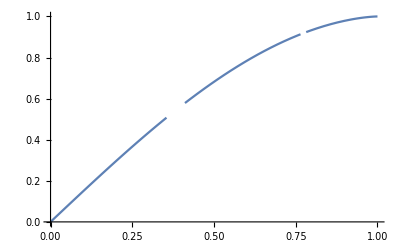

```mathematica
Plot[Np0NoPole[e,1],{e,0,1}]
```

```mathematica
p0NoPole[e,1]
```

$Aborted

```mathematica
Series
```

```mathematica
With[{e=.9},NpPlus2[e,1]]
```

-2.65957+2.87231×10^-11 ⅈ

```mathematica
With[{e=.5},NpPlus2[e,1]]
```

-1.52474+1.21784×10^-15 ⅈ

```mathematica
With[{e=.1},NpPlus2[e,1]]
```

-0.313767+8.11195×10^-16 ⅈ

```mathematica
With[{e=.9},NpPlus2[e,2]]
```

-3.61779+5.11583×10^-11 ⅈ

```mathematica
With[{e=.5},NpPlus2[e,2]]
```

2.66301-2.65102×10^-15 ⅈ

```mathematica
With[{e=.1},NpPlus2[e,2]]
```

6.12662-5.91228×10^-17 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.1269×10^-7}. NIntegrate obtained -6.59195×10^-16 + 4.16334×10^-16\ ⅈ and 1.50742×10^-12 for the integral and error estimates.

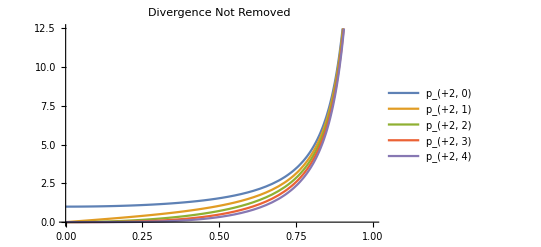

```mathematica
Plot[{Re[Np0[e,0]],Re[Np0[e,1]],Re[Np0[e,2]],Re[Np0[e,3]],Re[Np0[e,4]]},{e,0,1},PlotLegends->{"p_(+2, 0)","p_(+2, 1)","p_(+2, 2)","p_(+2, 3)","p_(+2, 4)"},PlotLabel->"Divergence Not Removed"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

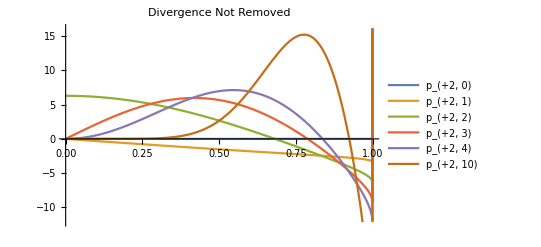

```mathematica
Plot[{Re[NpPlus2[e,0]],Re[NpPlus2[e,1]],Re[NpPlus2[e,2]],Re[NpPlus2[e,3]],Re[NpPlus2[e,4]],Re[NpPlus2[e,10]]},{e,0,1},PlotLegends->{"p_(+2, 0)","p_(+2, 1)","p_(+2, 2)","p_(+2, 3)","p_(+2, 4)","p_(+2, 10)"},PlotLabel->"Divergence Not Removed"]
```

```mathematica
Limit[pPlus2[e,1],e->1,Direction->"FromBelow"]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^2 does not converge on {0, 2\ π}.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^4 does not converge on {0, 2\ π}.

$Aborted

```mathematica
Multicolumn[Flatten[{"p_(2, 1)","p_(2, 2)","p_(2, 3)",Re[{With[{e=.9},NpPlus2[e,1]],With[{e=.9},NpPlus2[e,2]],With[{e=.9},NpPlus2[e,3]],With[{e=.99},NpPlus2[e,1]],With[{e=.99},NpPlus2[e,2]],With[{e=.99},NpPlus2[e,3]],With[{e=.999},NpPlus2[e,1]],With[{e=.999},NpPlus2[e,2]],With[{e=.999},NpPlus2[e,3]],With[{e=.9999},NpPlus2[e,1]],With[{e=.9999},NpPlus2[e,2]],With[{e=.9999},NpPlus2[e,3]],With[{e=.99999},NpPlus2[e,1]],With[{e=.99999},NpPlus2[e,2]],With[{e=.99999},NpPlus2[e,3]],With[{e=.999999},NpPlus2[e,1]],With[{e=.999999},NpPlus2[e,2]],With[{e=.999999},NpPlus2[e,3]]}]}],7]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0192414}. NIntegrate obtained 3.69061×10^10 + 4.68329×10^7\ ⅈ and 2.21771×10^13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0192414}. NIntegrate obtained 1.8453×10^10 + 2.34169×10^7\ ⅈ and 1.10886×10^13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0192414}. NIntegrate obtained 3.69061×10^10 + 9.36657×10^7\ ⅈ and 2.21771×10^13 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

p_(2, 1) | -2.65957 | -3.11682 | -3.28573 | -3.34483 | -3.36302 | 1.3884×10^15
p_(2, 2) | -3.61779 | -5.62128 | -6.1532 | -6.32247 | -6.37554 | 1.3884×10^15
p_(2, 3) | -3.78094 | -7.90384 | -8.9062 | -9.21271 | -9.30931 | 1.3884×10^15

```mathematica
Multicolumn[Flatten[{"p_(2, 1)/Pi","p_(2, 2)/2Pi","p_(2, 3)/3Pi",Re[{With[{e=.9999},NpPlus2[e,1]]/Pi,With[{e=.9999},NpPlus2[e,2]]/(2*Pi),With[{e=.9999},NpPlus2[e,3]]/(3*Pi)}]}],2]
```

p_(2, 1)/Pi | -1.06469
p_(2, 2)/2Pi | -1.00625
p_(2, 3)/3Pi | -0.977499

```mathematica
With[{e=.9999},NpPlus2[e,2]]
```

-6.32247+1.52245×10^-6 ⅈ

```mathematica
(2*Pi)/Re[With[{e=.9999},NpPlus2[e,2]]]
```

-0.993786

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

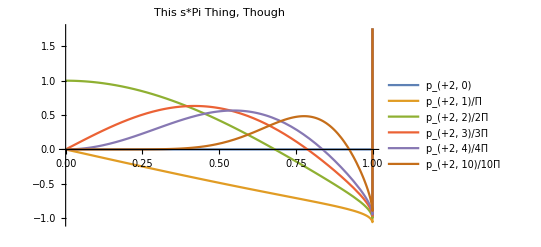

```mathematica
Plot[{Re[NpPlus2[e,0]],Re[NpPlus2[e,1]/Pi],Re[NpPlus2[e,2]/(2*Pi)],Re[NpPlus2[e,3]/(3*Pi)],Re[NpPlus2[e,4]/(4*Pi)],Re[NpPlus2[e,10]/(10*Pi)]},{e,0,1},PlotLegends->{"p_(+2, 0)","p_(+2, 1)/Π","p_(+2, 2)/2Π","p_(+2, 3)/3Π","p_(+2, 4)/4Π","p_(+2, 10)/10Π"},PlotLabel->"This s*Pi Thing, Though"]
```

```mathematica
With[{e=1},NpPlus2[e,2]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained 9.08033×10^46 - 40.9123\ ⅈ and 6.72143×10^45 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained 4.30486×10^109 - 3.70411×10^62\ ⅈ and 8.18445×10^108 for the integral and error estimates.

NIntegrate::inumri: The integrand ⅇ^2\ ⅈ\ (u - Sin[u])\ Cos[2\ u]/(1 - Cos[u])^4 has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0., 1.35186×10^-14}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained -2.46151×10^94 + 2.42142×10^47\ ⅈ and 3.40473×10^93 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

9.08033×10^46-40.9123 ⅈ

```mathematica
With[{e=.9999},NpPlus2[e,1]]
```

-3.34483+4.38363×10^-8 ⅈ

```mathematica
With[{e=.9999},NpPlus2[e,3]]
```

-9.21271+7.36371×10^-8 ⅈ

```mathematica
(3*Pi)/Re[With[{e=.9999},NpPlus2[e,3]]]
```

-1.02302

```mathematica
With[{e=.999},NpPlus2NP[e,2]]
```

-0.000549946+6.76786×10^-14 ⅈ

```mathematica
With[{e=1},NpPlus2NP[e,2]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained 9.08033×10^46 - 40.9123\ ⅈ and 6.72143×10^45 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained 4.30486×10^109 - 3.70411×10^62\ ⅈ and 8.18445×10^108 for the integral and error estimates.

NIntegrate::inumri: The integrand ⅇ^2\ ⅈ\ (u - Sin[u])\ Cos[2\ u]/(1 - Cos[u])^4 has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0., 1.35186×10^-14}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853071795735487831669907467342744961093736152567078680555857}. NIntegrate obtained -2.46151×10^94 + 2.42142×10^47\ ⅈ and 3.40473×10^93 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

0.+0. ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

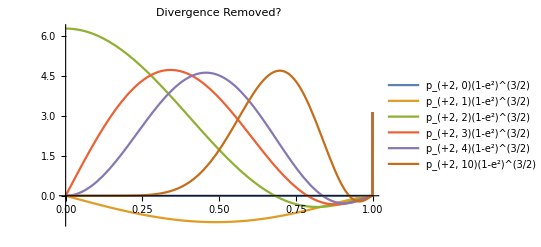

```mathematica
Plot[{Re[NpPlus2NP[e,0]],Re[NpPlus2NP[e,1]],Re[NpPlus2NP[e,2]],Re[NpPlus2NP[e,3]],Re[NpPlus2NP[e,4]],Re[NpPlus2NP[e,10]]},{e,0,1},PlotLegends->{"p_(+2, 0)(1-e^2)^(3/2)","p_(+2, 1)(1-e^2)^(3/2)","p_(+2, 2)(1-e^2)^(3/2)","p_(+2, 3)(1-e^2)^(3/2)","p_(+2, 4)(1-e^2)^(3/2)","p_(+2, 10)(1-e^2)^(3/2)"},PlotLabel->"Divergence Removed?"]
```

```mathematica
Limit[((1-e^2)^(3/2))*pPlus2[e,1],e->1,Direction->"FromBelow"]
```

```mathematica
FullSimplify[Series[2*Pi*p0[e,1]*((1-e^2)^(3/2)),{e,0,10}]]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^2 does not converge on {0, 2\ π}.

3 π e-(9 π e^3)/8+(9 π e^5)/64-(19 π e^7)/3072-(133 π e^9)/81920+O[e]^11

```mathematica
Series[pPlus2[e,0]*((1-e^2)^(3/2)),{e,0,10}]
```

0

```mathematica
Series[pPlus2[e,1]*((1-e^2)^(3/2)),{e,0,10}]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of ⅇ^ⅈ\ (u - e\ Sin[u])/(-1 + e\ Cos[u])^2 does not converge on {0, 2\ π}.

$Aborted

## Shape of m=-2 feat. Justin Bieber

```mathematica
Plot[{Re[NpMinus2[e,0]],Re[NpMinus2[e,1]],Re[NpMinus2[e,2]],Re[NpMinus2[e,3]],Re[NpMinus2[e,4]],Re[NpMinus2[e,10]]},{e,0,1},PlotLegends->{"p_(-2, 0)","p_(-2, 1)","p_(-2, 2)","p_(-2, 3)","p_(-2, 4)","p_(-2, 10)"},PlotLabel->"Divergence Not Removed"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

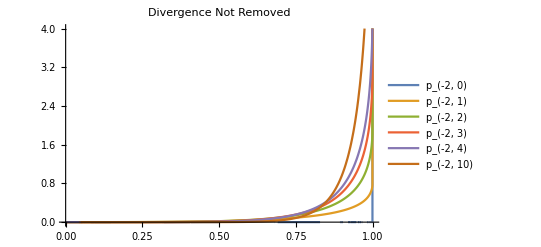

```mathematica
Plot[{Re[NpMinus2[e,0]],Re[NpMinus2[e,1]],Re[NpMinus2[e,2]],Re[NpMinus2[e,3]],Re[NpMinus2[e,4]],Re[NpMinus2[e,10]]},{e,0,1},PlotLegends->{"p_(-2, 0)","p_(-2, 1)","p_(-2, 2)","p_(-2, 3)","p_(-2, 4)","p_(-2, 10)"},PlotLabel->"Divergence Not Removed",PlotRange->{0,4}]
```

```mathematica
Multicolumn[Flatten[{"p_(-2, 1)","p_(-2, 2)","p_(-2, 3)",Re[{With[{e=.1},NpMinus2[e,1]],With[{e=.1},NpMinus2[e,2]],With[{e=.1},NpMinus2[e,3]],With[{e=.5},NpMinus2[e,1]],With[{e=.5},NpMinus2[e,2]],With[{e=.5},NpMinus2[e,3]],With[{e=.9},NpMinus2[e,1]],With[{e=.9},NpMinus2[e,2]],With[{e=.9},NpMinus2[e,3]],With[{e=.999},NpMinus2[e,1]],With[{e=.999},NpMinus2[e,2]],With[{e=.999},NpMinus2[e,3]],With[{e=.9999},NpMinus2[e,1]],With[{e=.9999},NpMinus2[e,2]],With[{e=.9999},NpMinus2[e,3]]}]}],6]
```

p_(-2, 1) | 0.000131806 | 0.0197906 | 0.233929 | 0.728321 | 0.787001
p_(-2, 2) | 0.0000263647 | 0.0199208 | 0.4513 | 1.73673 | 1.89759
p_(-2, 3) | 4.00106×10^-6 | 0.0148864 | 0.608663 | 2.78784 | 3.07296

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0000241858}. NIntegrate obtained -2.49366×10^-16 and 1.59399×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.50367}. NIntegrate obtained 1.73472×10^-17 and 3.8204×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

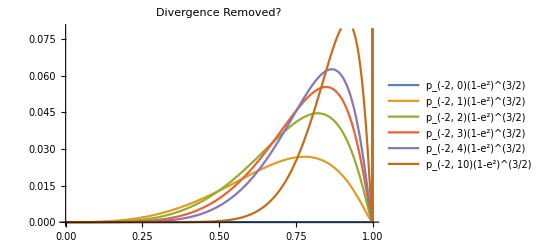

```mathematica
Plot[{Re[NpMinus2NP[e,0]],Re[NpMinus2NP[e,1]],Re[NpMinus2NP[e,2]],Re[NpMinus2NP[e,3]],Re[NpMinus2NP[e,4]],Re[NpMinus2NP[e,10]]},{e,0,1},PlotLegends->{"p_(-2, 0)(1-e^2)^(3/2)","p_(-2, 1)(1-e^2)^(3/2)","p_(-2, 2)(1-e^2)^(3/2)","p_(-2, 3)(1-e^2)^(3/2)","p_(-2, 4)(1-e^2)^(3/2)","p_(-2, 10)(1-e^2)^(3/2)"},PlotLabel->"Divergence Removed?",PlotRange->{0,0.1}]
```

```mathematica
FullSimplify[p -2 0 or something]
```

```mathematica
Multicolumn[Flatten[{"p_(-2, 1)(1-e^2)^(3/2)","p_(-2, 2)(1-e^2)^(3/2)","p_(-2, 3)(1-e^2)^(3/2)",Re[{With[{e=.1},NpMinus2NP[e,1]],With[{e=.1},NpMinus2NP[e,2]],With[{e=.1},NpMinus2NP[e,3]],With[{e=.5},NpMinus2NP[e,1]],With[{e=.5},NpMinus2NP[e,2]],With[{e=.5},NpMinus2NP[e,3]],With[{e=.9},NpMinus2NP[e,1]],With[{e=.9},NpMinus2NP[e,2]],With[{e=.9},NpMinus2NP[e,3]],With[{e=.999},NpMinus2NP[e,1]],With[{e=.999},NpMinus2NP[e,2]],With[{e=.999},NpMinus2NP[e,3]],With[{e=.9999},NpMinus2NP[e,1]],With[{e=.9999},NpMinus2NP[e,2]],With[{e=.9999},NpMinus2NP[e,3]]}]}],6]
```

p_(-2, 1)(1-e^2)^(3/2) | 0.000129834 | 0.0128544 | 0.0193738 | 0.0000650942 | 2.22581×10^-6
p_(-2, 2)(1-e^2)^(3/2) | 0.0000259702 | 0.012939 | 0.0373762 | 0.000155221 | 5.36681×10^-6
p_(-2, 3)(1-e^2)^(3/2) | 3.94119×10^-6 | 0.00966901 | 0.0504089 | 0.000249165 | 8.69098×10^-6

It kind of looks like -2 is just going to be consistently smaller than +2; maybe even at its maximum value it’ll be negligible?
Except +2 is specifically small near e=1. But still. I guess with that in mind I don’t need to know the maximum, but it might dominate. I can do for both. Or something. Yeah.
At the very least it kind of looks like for low e, we can drop -2 basically entirely, and maybe drop both of them past some value s. Anyway.

```mathematica
FindMaximum[Limit[NpMinus2NP[e,s],s->Infinity],{e,.9}]
```

NIntegrate::inumr: The integrand ⅇ^ⅈ\ s\ (u - e\ Sin[u])/(1 - e\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate::inumr: The integrand ⅇ^ⅈ\ s\ (u - e\ Sin[u])/(1 - e\ Cos[u])^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

$Aborted

## I should organize this better

```mathematica
pEmEs[e_,m_,s_]:=Integrate[,{u,0,2*Pi}]
```

Okay, so the hard thing was first getting the thing in the right form, so I’m going to try using With

```mathematica
With[,Cos[m*]
```